```mathematica
data = ColorConvert[ (*shape*)-Graphics- , "Grayscale" ] // ImageData  ;
data = Map[ #==1 &,  data[[All,All, 2]], {2}] ;
dd = data // Dimensions ;
```

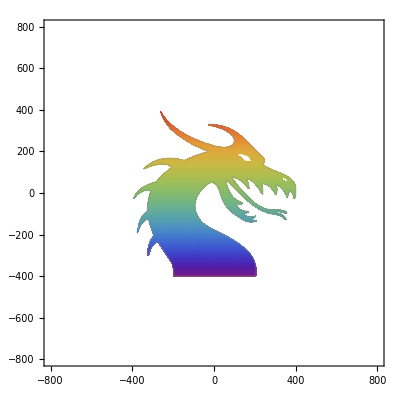

```mathematica
ClearAll[checkAgainstRange] ;
checkAgainstRange::usage = "This is to deal with InputForm Manipulators, that allow non-numeric values to be passed, or values that exceed the range specified in the Manipulator." ;
checkAgainstRange[v_,default_,lowerLimit_, upperLimit_, typeFunc_ : NumberQ] := 
Module[{result},
result = If [ typeFunc[v],v, default] ;

result = If [ result <= upperLimit, result,default ] ;
result = If [ result >= lowerLimit, result,default ] ;

result
] ;

ClearAll[f]
f[point_List] := Module[{ dr, scaled, r, s},
dr = Take[ dd, 2] ;
scaled = Floor[ {{0, -1},{1, 0}}. point  + (dr + {1,1}) /2] ;
{r, s} = checkAgainstRange[scaled[[#]], 1, 1, dr[[#]]] &/@ Range[2];

data[[r]][[s]]
]

ClearAll[ followPointWithinConeToTop]
followPointWithinConeToTop::usage = "For a set of coordinates, point = {x, y, z}, follow the point {x,y} in the plane at height z to a height of h (either on the interior or the exterior of a cone)" ;
followPointWithinConeToTop[point_List, h_] := Module[{planeProj, z},
planeProj = Take[point, 2] ;
z = point // Last ;

h planeProj / z
]

(*RegionPlot[ f[{x, y}], {x, -dd[[1]], dd[[1]]}, {y, -dd[[2]],dd[[2]]}
(*, PlotRange -> Full*)
, PerformanceGoal -> "Quality"
, PlotPoints -> 40
, ColorFunction->"Rainbow" ] *)
RegionPlot[ f[{x, y}], {x, -dd[[1]], dd[[1]]}, {y, -dd[[2]],dd[[2]]}
(*, PlotRange -> Full*)
, PerformanceGoal -> "Quality"
, PlotPoints -> 200
, MaxRecursion->1
, ColorFunction->"Rainbow" ]
```

```mathematica
(*ContourPlot[1, {x, -5, 5}, {y, -5, 5}
,
RegionFunction ->  Function[{x,y},2<x^2+y^2<9]
, MaxRecursion->0
, PlotPoints -> 11
]*)
```

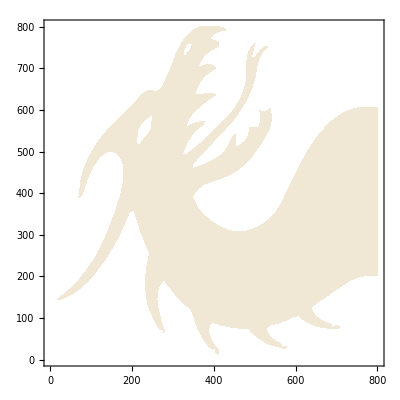

```mathematica
ContourPlot[1, {x, 1, 800}, {y, 1, 800}
,
RegionFunction ->  Function[{x,y},data[[Floor[x]]][[Floor[y]]]]
, MaxRecursion->0
, PlotPoints -> 100
(*, ColorFunction->"Red" *)
]
```

```mathematica
Module[{t},
(*t = Flatten[ Table[ {x,y,data[[x]][[y]]}, {x, 1, dd[[1]], 100}, {y, 1, dd[[2]], 100}], 1] ;*)
(*ListPlot[ data
(*,RegionFunction ->  Function[{x,y},data[[Floor[x]]][[Floor[y]]]]*)
(*, MaxRecursion->0
, PlotPoints -> 100*)
(*, ColorFunction->"Red" *)
]*)
0
]
```

-Graphics-

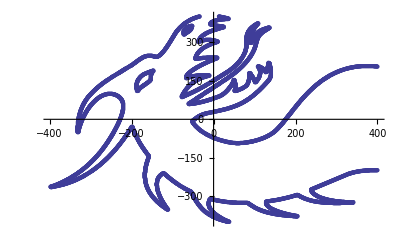

```mathematica
(* http://mathematica.stackexchange.com/a/48684/10 *)
image = Import["http://imgur.com/HhsMeDc.png"] // AlphaChannel;

(*ImageLevels[ image, 10 ] 
b = Binarize[ image ] 
ImageLevels[ b ]
*)
(*b = Binarize[ image, 0.1 ] ;
ImageLevels[ b ]
*)

data = image   // EdgeDetect // (*ColorNegate //*) ImageData ;
{wx, wy}  = data // Dimensions ;
(*dataOffset = {-#2+wy/2,-#1+wx/2(*,data[[##]]*)}&@@@Position[data,1] ;*)
dataOffset = {#1 - wx/2, #2 - wy/2}&@@@Position[data,1] ;
(*t = Table[ dataOffset i, {i, 0.1, 1, 0.1}]*)
t = Flatten[ Table[ {(i/wx) #[[1]], (i/wx)#[[2]], i} &/@ dataOffset, {i, 1, wx, 50}], 1] ;

(*ListPlot[ dataOffset(*, PerformanceGoal->"Quality"*)
 (*, PlotRange -> 2{{-wy, wy}, {-wx, wx}}/3 *)
,PlotStyle->Directive[PointSize[0.005]]
, PlotRange -> {{-wx/2, wx/2}, {-wy/2, wy/2}}
]
*)
(*ListPlot3D[ t ]*)


(*dataOffset // Dimensions*)


(*Take[ dataOffset, 20 ] *)
```

```mathematica
(*Clear[x, y, t]
(* ;*)

t = {{1,1,0},{1,2,1},{1,3,0},{1,4,0},{1,5,1},{1,6,0},{1,7,0},{1,8,0},{1,9,1},{1,10,0}} *)

(*Select[ t, #[[3]] == 1 &]*)

(*data = Array[ RandomInteger[1] &, {4,4}]
{wx, wy} = data // Dimensions ;
t = Flatten[ Table[ {x - wx/2, y - wy/2, data[[x]][[y]]}, {x, 1, wx}, {y, 1, wy}], 1]
Select[ t, #[[3]] == 1 &]*)

(*data // MatrixForm
Position[data, 1]
data[[##]]&@@@Position[data,1]
s = SparseArray[data] // FullForm
Position[s, 1]
Unitize@Subtract[data,1]
s = SparseArray[Unitize@Subtract[data,1],Automatic,1];
pos=s["NonzeroPositions"]*)
```

```mathematica
(*dx = RandomInteger[ 1, {3,3}] ;
dx // MatrixForm
d2 = Position[dx,1] 
(*{#[[1]], #[[2]], 3} &/@ d2*)
Flatten[ Table[ {i #[[1]], i#[[2]], i} &/@ d2, {i, 0.1, 1, 0.1}], 1]*)
```

```mathematica
ListPlot3D[ t ]
```

-Graphics3D-

```mathematica
(*Take[ t, 20 ]*)
```

{{-39.8,-26.3,0.1},{-39.8,-26.2,0.1},{-39.7,-26.4,0.1},{-39.7,-26.2,0.1},{-39.6,-26.4,0.1},{-39.6,-26.2,0.1},{-39.6,-26.1,0.1},{-39.5,-26.4,0.1},{-39.5,-26.3,0.1},{-39.5,-26.1,0.1},{-39.4,-26.3,0.1},{-39.4,-26.1,0.1},{-39.4,-26.,0.1},{-39.3,-26.3,0.1},{-39.3,-26.,0.1},{-39.2,-26.2,0.1},{-39.2,-26.,0.1},{-39.2,-25.9,0.1},{-39.1,-26.2,0.1},{-39.1,-25.9,0.1}}

```mathematica
(*ListContourPlot3D[ t ]*)
```